## Equilibrium potentials

Formal potential for protonated species (in V): (pKa1-Ox, pKa2-Red)

```mathematica
Efp[Ef_,pKaOx_,pKaRed_]:=Ef+0.058(pKaRed-pKaOx);
```

Аpparent formal potential (in V):

```mathematica
Efapp[Ef_,pKaOx_,pKaRed_,pH_]:=Ef+0.058Log10[(1+10^(-pH+pKaRed))/(1+10^(-pH+pKaOx))];
```

```mathematica
Efp[0,3,11]
```

0.464

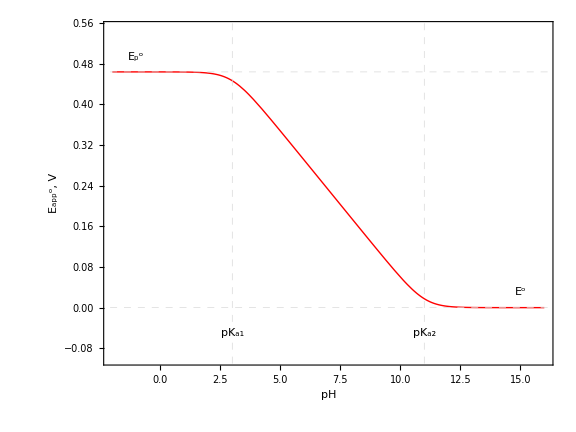

```mathematica
Ef=0;
pKaOx=3;
pKaRed=11;
Efprot=Efp[Ef,pKaOx,pKaRed];
Plot[Efapp[Ef,pKaOx,pKaRed,pH],{pH,-2,16},
PlotRange->{-0.1,0.55},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
Axes->False,Frame->True,
FrameLabel->{"pH","E_app^o, V"},
FrameStyle->Directive[Black,Thick],
GridLines->{{pKaOx,pKaRed},{Ef,Efprot}},
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick],
Epilog->{
Text["E^o",{15,0.03}],Text["E_p^o",{-1,Efprot+0.03}],
Text["pK_a1",{pKaOx,-0.05},Background->White],
Text["pK_a2",{pKaRed,-0.05},Background->White]
}
]
```

## Apparent standard rate constants

### Laviron step-wise model

```mathematica
ksapp[pKa1_,pKa2_,ksp_,ks_,pH_]:=ks(1+10^-pH ksp/ks(10^(-pKa1-pKa2))^(-1/2))(1+10^(-pH+pKa1))^(-1/2)(1+10^(-pH+pKa2))^(-1/2);
```

```mathematica
Manipulate[
Plot[Log@ksapp[pKa1,pKa2,ksp,ks,pH],{pH,-2,16},
PlotRange->All,
GridLines->{{pKa1,pKa2},{ksp,ks}},
Axes->False,Frame->True,
FrameLabel->{"pH","ln(k_(s, app))"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thick],
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick],
Epilog->{
Text["k_sp",{0,Log@ksp},Background->White],Text["k_s",{15,Log@ks},Background->White],
Text["pK_a1",{pKa1,Log@Min[Table[ksapp[pKa1,pKa2,ksp,ks,x],{x,0,14,1}]]},Background->White],
Text["pK_a2",{pKa2,Log@Min[Table[ksapp[pKa1,pKa2,ksp,ks,x],{x,0,14,1}]]},Background->White],
Text["(k_(s, app))/(k_(s, app)) = "<>ToString[(N@ksapp[pKa1,pKa2,ksp,ks,3])/(N@ksapp[pKa1,pKa2,ksp,ks,5])],{7,5},Background->White]
}
],
{{pKa1,2,"pK_a1"},-2,16},
{{pKa2,12,"pK_a2"},-2,16},
{{ksp,50,"k_s1"},1,1000},
{{ks,350,"k_s2"},1,1000},
LabelStyle->Large
]
```

Apparent transfer coefficient:

```mathematica
αapp=-1/f D[Log[10^(-pH+pKa1)Exp[-(αp+(x-Ep0)/(2λp)) f (x-Ep0)]+Exp[-(α+(x-E0)/(2λ)) f(x-E0)]],x]
```

-(ⅇ^(f (-E0+x) (-α-(-E0+x)/(2 λ))) (f (-α-(-E0+x)/(2 λ))-(f (-E0+x))/(2 λ))+10^(-pH+pKa1) ⅇ^(f (-Ep0+x) (-αp-(-Ep0+x)/(2 λp))) (f (-αp-(-Ep0+x)/(2 λp))-(f (-Ep0+x))/(2 λp)))/((ⅇ^(f (-E0+x) (-α-(-E0+x)/(2 λ)))+10^(-pH+pKa1) ⅇ^(f (-Ep0+x) (-αp-(-Ep0+x)/(2 λp)))) f)

```mathematica
FullSimplify[αapp,Assumptions->{f>0,pH∈Reals,pKa1∈Reals,E0∈Reals,Ep0∈Reals,α>0,αp>0,λp>0,λ>0}]
```

$Aborted

```mathematica
αApp[x_,αp_,λp_,α_,λ_,Ep0_,E0_,pKa1_,pH_]:=Module[
{f=Log[10]/0.058},
-(ⅇ^(f (-E0+x) (-α-(-E0+x)/(2 λ))) (f (-α-(-E0+x)/(2 λ))-(f (-E0+x))/(2 λ))+10^(-pH+pKa1) ⅇ^(f (-Ep0+x) (-αp-(-Ep0+x)/(2 λp))) (f (-αp-(-Ep0+x)/(2 λp))-(f (-Ep0+x))/(2 λp)))/((ⅇ^(f (-E0+x) (-α-(-E0+x)/(2 λ)))+10^(-pH+pKa1) ⅇ^(f (-Ep0+x) (-αp-(-Ep0+x)/(2 λp)))) f)];
```

```mathematica
Manipulate[
Plot[αApp[Efapp[0,pK1,pK2,pH],αp,λp,α,λ,Efp[0,pK1,pK2],0,pK1,pH],{pH,0,14},
PlotRange->{0,1},
GridLines->{{pK1,pK2},{αp,α}},
Axes->False,Frame->True,
FrameLabel->{"pH","α_app"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thick],
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick],
Epilog->{
Text["α_p",{1,αp},Background->White],Text["α",{13,α},Background->White],
Text["pK_a1",{pK1,0.1},Background->White],
Text["pK_a2",{pK2,0.1},Background->White]
}
],
{{pK1,3},0,14},
{{pK2,11},0,14},
{{αp,0.6},0,1},
{{α,0.4},0,1},
{{λp,1},0.1,100,0.1},
{{λ,1},0.1,100,0.1}
]
```

350

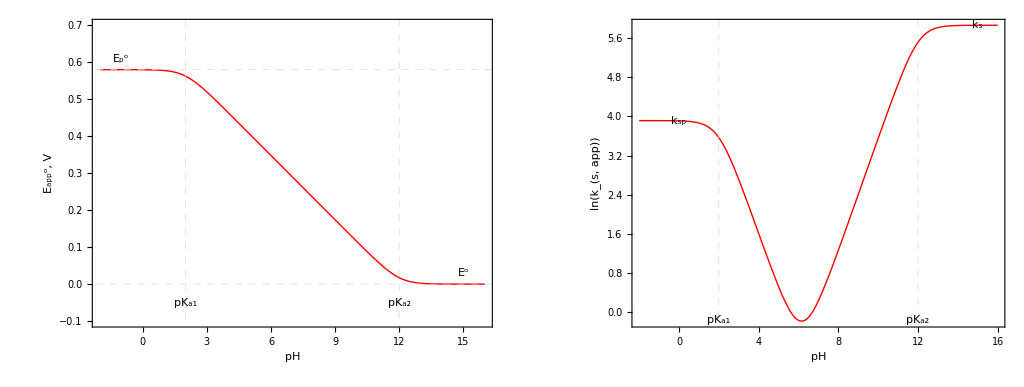

```mathematica
Ef=0;
pKaOx=2;
pKaRed=12;
ks=50;
ksp=350
Efprot=Efp[Ef,pKaOx,pKaRed];
GraphicsRow[{
Plot[Efapp[Ef,pKaOx,pKaRed,pH],{pH,-2,16},
PlotRange->{-0.1,0.7},
AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
Axes->False,Frame->True,
FrameLabel->{"pH","E_app^o, V"},
FrameStyle->Directive[Black,Thick],
GridLines->{{pKaOx,pKaRed},{Ef,Efprot}},
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick],
Epilog->{
Text["E^o",{15,0.03}],Text["E_p^o",{-1,Efprot+0.03}],
Text["pK_a1",{pKaOx,-0.05},Background->White],
Text["pK_a2",{pKaRed,-0.05},Background->White]
}
],
Plot[Log@ksapp[pKaOx,pKaRed,ks,ksp,pH],{pH,-2,16},
PlotRange->All,
GridLines->{{pKaOx,pKaRed},{ks,ksp}},
Axes->False,Frame->True,
FrameLabel->{"pH","ln(k_(s, app))"},
AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thick],
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick],
Epilog->{
Text["k_sp",{0,Log@ks},Background->White],Text["k_s",{15,Log@ksp},Background->White],
Text["pK_a1",{pKaOx,Log@Min[Table[ksapp[pKaOx,pKaRed,ks,ksp,x],{x,0,14,1}]]},Background->White],
Text["pK_a2",{pKaRed,Log@Min[Table[ksapp[pKaOx,pKaRed,ks,ksp,x],{x,0,14,1}]]},Background->White]
}
]
},ImageSize->1024]
```

### Yogi’s model for GCC

```mathematica
ksappY[ks1_,ks2_,α1_,α2_,pH_]:=ks1 10^(-α1 pH)+ks2 10^((1-α2)(pH-14));
```

```mathematica
Manipulate[
LogPlot[ksappY[ks1,ks2,α1,α2,pH],{pH,-2,16},
PlotRange->All,
GridLines->{None,{ks1,ks2}},
Axes->False,Frame->True,
FrameLabel->{"pH","ln(k_(s, app))"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thick],
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick]
],
{{α1,0.5,"α_1"},0,1},
{{α2,0.5,"α_2"},0,1},
{{ks1,50,"k_s1"},1,100},
{{ks2,50,"k_s2"},1,100},
LabelStyle->Large
]
```

## Cathodic effective first order PCET rate constant with buffer

```mathematica
kc[pH_,pKa_]:=1/(1+10^(pH-pKa));
```

```mathematica
Manipulate[
LogPlot[kc[pH,pKa],{pH,-4,14},
PlotRange->All,
GridLines->{{pKa},None},
Axes->False,Frame->True,
FrameLabel->{"pH","(k̃)^PCET/(k^PCET K C_B)"},
ImageSize->Large,AspectRatio->0.75,
BaseStyle->{20,FontFamily->"Helvetica"},
FrameStyle->Directive[Black,Thick],
GridLinesStyle->Directive[Dashed,Thick],
PlotStyle->Directive[Red,Thick]
],
{{pKa,3},0,14},
LabelStyle->Large
]
```